# Results from “On the importance of reproducible scientific computations in mathematical epidemiology”

This Mathematica Notebook is a supplementary material to the paper “On the importance of reproducible scientific computations in mathematical epidemiology”. It contains some of the calculations and illustrations appearing in the paper .

## I)SIR with B(s,i)=β s /(1+μ i) and T(i)=η w i/(i+w) preliminaries.

```mathematica
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];
AppendTo[$Path, FileNameJoin[{$HomeDirectory, "Dropbox", "EpidCRNmodels"}]];<<EpidCRN`;
Needs["HopfR1`"];

cZF={γs->0,γr->0,is->0,ir->γ}; cir={ir->γ-is};cis={is->γ-ir};


RN = {0 -> "s",
      "s" + "i" -> 2*"i",
      "s"  -> "r",
      "r"  -> "s",
       "i" -> "s",
       "i"->"r",
      "s" -> 0,
      "i" -> 0,
      "r" -> 0};

rts={Λ, s i β/(1+ i ξ), s γs, r γr, i is, i(ir+η ω/(i+ω)), μ s, (μ+δ) i, μ r};

{ngm, Jx, Jy, mSi, R0, bdp, RHS, var, cp}= bdAnalG[RN, rts];par=Par[RHS,var];

poliG=Grobpol[RHS,var,par,{2}][[1,1]]//Factor (*Reduced polynomial with respect to i using Grobner Basis*);
Print["poliG=  ", poliG]


poli=Collect[Factor[poliG[[3]]/(μ)],i];
{Co,B,A}=CoefficientList[poli,i];
```

RHS= (i is+r γr-s γs+Λ-s μ-(i s β)/(1+i ξ)
-i is-i (δ+μ)+(i s β)/(1+i ξ)-i (ir+(η ω)/(i+ω))
-r γr+s γs-r μ+i (ir+(η ω)/(i+ω))) has var {s,i,r} par{ir,is,β,γr,γs,δ,η,Λ,μ,ξ,ω}

minimal siphons {{i}} Check siphon={True}

Species names (spe): {s,i,r}

Variables (var): {s,i,r}

Minimal siphons (mS): {{i}}

Infection species positions (mSi): {{2}}

All infection positions (inf): {2}

Siphon 1 contains species: {i} at positions: {2} corresponding to variables: {i}

DFE solution E0: {r→(γs Λ)/(μ (γr+γs+μ)),s→(Λ (γr+μ))/(μ (γr+γs+μ)),i→0}

NGM K= ((s β)/(ir+is+δ+η+μ)) =((s β)/(ir+is+δ+η+μ))

Reproduction functions R0A: {(s β)/(ir+is+δ+η+μ)}

R0 at DFE: (s β)/(ir+is+δ+η+μ)

Processing siphon 1: positions {2} setting variables {i} to zero

Boundary equations: {r γr-s γs+Λ-s μ==0,True,-r γr+s γs-r μ==0}

Variables to solve for: {r,s}

Found 1 solutions for boundary 1

Adding boundary point: {r→(γs Λ)/(μ (γr+γs+μ)),s→(Λ (γr+μ))/(μ (γr+γs+μ)),i→0}

Number of boundary points found: 1

Boundary points:

Point 1: {r→(γs Λ)/(μ (γr+γs+μ)),s→(Λ (γr+μ))/(μ (γr+γs+μ)),i→0}

poliG=  i (1+i ξ) (i^2 β γr δ-i β γr Λ+i^2 ir β μ+i ir γr μ+i is γr μ+i^2 β γr μ+i ir γs μ+i is γs μ+i^2 β δ μ+i γr δ μ+i γs δ μ-i β Λ μ+i ir μ^2+i is μ^2+i^2 β μ^2+i γr μ^2+i γs μ^2+i δ μ^2+i μ^3+i^2 ir γr μ ξ+i^2 is γr μ ξ+i^2 ir γs μ ξ+i^2 is γs μ ξ+i^2 γr δ μ ξ+i^2 γs δ μ ξ+i^2 ir μ^2 ξ+i^2 is μ^2 ξ+i^2 γr μ^2 ξ+i^2 γs μ^2 ξ+i^2 δ μ^2 ξ+i^2 μ^3 ξ+i β γr δ ω-β γr Λ ω+i ir β μ ω+ir γr μ ω+is γr μ ω+i β γr μ ω+ir γs μ ω+is γs μ ω+i β δ μ ω+γr δ μ ω+γs δ μ ω+i β η μ ω+γr η μ ω+γs η μ ω-β Λ μ ω+ir μ^2 ω+is μ^2 ω+i β μ^2 ω+γr μ^2 ω+γs μ^2 ω+δ μ^2 ω+η μ^2 ω+μ^3 ω+i ir γr μ ξ ω+i is γr μ ξ ω+i ir γs μ ξ ω+i is γs μ ξ ω+i γr δ μ ξ ω+i γs δ μ ξ ω+i γr η μ ξ ω+i γs η μ ξ ω+i ir μ^2 ξ ω+i is μ^2 ξ ω+i γr μ^2 ξ ω+i γs μ^2 ξ ω+i δ μ^2 ξ ω+i η μ^2 ξ ω+i μ^3 ξ ω)

#### The two dimensional ZF- model:

```mathematica
RHSZF=RHS/.cZF//FullSimplify;parZ=Par[RHSZF,var];
Print["in teh ZF case: RHSZF (s'
i'
r')= " , RHSZF//MatrixForm]

RHSZ2= Drop[RHSZF,-1];(*The remaining equations do not depend on r*)
parZ2=Par[RHSZ2,{s,i}]; ifacZ=Simplify[RHSZ2[[2]]/i];
Print["For 2-dim case, we have ( s'
i')=",RHSZ2//MatrixForm," with ",Length[parZ2], " parameters:", parZ2]

(*Let's compute some useful quantities (Jacobian, Det, and Trace)*)

jacZ2=Grad[RHSZ2,{s,i}]//FullSimplify;
detZ2=Det[jacZ2]//FullSimplify;
Print["2 dim jac (ZF case)=",jacZ2//MatrixForm]
trZ2=Tr[jacZ2];

(*Elimination of s via plugging, for trace and det*)
Print["s formula cs from first and sec eqs are"]
cs=Flatten[Solve[RHSZ2[[1]]==0,s]]
cs2=Flatten[Solve[ifacZ==0,s]]
se02=s/.cs2;

deti=(detZ2/.cs2)//Factor;
Print[" det after elim of s=", deti]
nudet=Factor[Numerator[deti]];


Print["trZ2= ",trZ2]
tri=Together[(trZ2/.cs2)]//Factor;
Print[" tr after elim of s is ", tri]
ie=i/.Solve[poli==0,i];ic0=(-B/(2 A));

detE=deti /.i->ic0 (* det when i=-B/(2A) *);
detE2=deti/.i->ie[[2]];
detE1=deti/.i->ie[[1]];
trE2=tri/.i->ie[[2]];
trE1=tri/.i->ie[[1]];


Print["cofs of simpl. pol in ZF case ",{Co,B,A}/.cZF//FullSimplify]
Print["Dis= ",dis=B^2 -4 A Co/.cZF//FullSimplify]
```

in teh ZF case: RHSZF (s'
i'
r')= (Λ-s μ-(i s β)/(1+i ξ)
-i (δ+μ)+(i s β)/(1+i ξ)-i (γ+(η ω)/(i+ω))
-r μ+i (γ+(η ω)/(i+ω)))

For 2-dim case, we have ( s'
i')=(Λ-s μ-(i s β)/(1+i ξ)
-i (δ+μ)+(i s β)/(1+i ξ)-i (γ+(η ω)/(i+ω))) with 8 parameters:{β,γ,δ,η,Λ,μ,ξ,ω}

2 dim jac (ZF case)=(-μ-(i β)/(1+i ξ) | -(s β)/(1+i ξ)^2
(i β)/(1+i ξ) | -γ-δ-μ+(s β)/(1+i ξ)^2-(η ω^2)/(i+ω)^2)

s formula cs from first and sec eqs are

{s→(Λ (1+i ξ))/(i β+μ+i μ ξ)}

{s→((1+i ξ) (γ+δ+μ+(η ω)/(i+ω)))/β}

det after elim of s=1/((1+i ξ) (i+ω)^2)i (i^2 β γ+i^2 β δ+i^2 β μ+i^2 γ μ ξ+i^2 δ μ ξ+i^2 μ^2 ξ+2 i β γ ω+2 i β δ ω+2 i β μ ω-η μ ω+2 i γ μ ξ ω+2 i δ μ ξ ω+2 i μ^2 ξ ω+β γ ω^2+β δ ω^2+β η ω^2+β μ ω^2+γ μ ξ ω^2+δ μ ξ ω^2+η μ ξ ω^2+μ^2 ξ ω^2)

trZ2= -γ-δ-2 μ+(s β)/(1+i ξ)^2-(i β)/(1+i ξ)-(η ω^2)/(i+ω)^2

tr after elim of s is -1/((1+i ξ) (i+ω)^2)(i^3 β+i^2 μ+i^3 γ ξ+i^3 δ ξ+2 i^3 μ ξ+2 i^2 β ω-i η ω+2 i μ ω+2 i^2 γ ξ ω+2 i^2 δ ξ ω+4 i^2 μ ξ ω+i β ω^2+μ ω^2+i γ ξ ω^2+i δ ξ ω^2+i η ξ ω^2+2 i μ ξ ω^2)

cofs of simpl. pol in ZF case {(-β Λ+μ (γ+δ+η+μ)) ω,-β Λ+μ (γ+δ+μ)+(γ+δ+η+μ) (β+μ ξ) ω,(γ+δ+μ) (β+μ ξ)}

Dis= -4 (γ+δ+μ) (-β Λ+μ (γ+δ+η+μ)) (β+μ ξ) ω+(-β Λ+μ (γ+δ+μ)+(γ+δ+η+μ) (β+μ ξ) ω)^2

#### Useful Quantities for Bifurcation map & Numerical conditions:

```mathematica
cut=Thread[{Λ,δ,γ,β,ξ,μ,γr,γs,is,ir,Subscript[v, 2],Subscript[v, 1],Subscript[V, 2]}->{16,2/10,12/100,1/100,1/1000,12/100,0,0,0,γ,μ+γ+δ,β+ μ ξ,μ+γ+δ+η}];
cutF=Thread[{Λ,δ,γ,β,ξ,μ,Subscript[v, 2],Subscript[v, 1],Subscript[V, 2]}->{16,2/10,12/100,1/100,1/1000,1/10,μ+γ+δ,β+ μ ξ,μ+γ+δ+η}];
paramGc=Thread[{Λ,δ,γ,β,ξ,μ,Subscript[v, 2],Subscript[v, 1],Subscript[V, 2]}->{1/2,2/10,1/10,2/10,7/100,1/10,(μ+γ+δ),(β+ μ ξ),μ+γ+δ+η}];
(*cuteters of Figure 4 in Zhou Fan*)
ParNumCheck=Thread[{ω,α,η}->{7/64,179/64,ω/α}];
Print["test cNN="]
cNN=Join[ParNumCheck,cut]
equi=Solve[Thread[RHS==0],var];
equi//.cNN//N
Length[equi]


cv2={Subscript[v, 2]->(μ+γ+δ)};cv1={Subscript[v, 1]->(β+ μ ξ)};cV2={Subscript[V, 2]->Subscript[v, 2]+η,Subscript[v, 2]->(μ+γ+δ)};
cv={ξ ->(Subscript[v, 1]-β)/μ,δ ->Subscript[v, 2]-(μ+γ),η->Subscript[V, 2]-Subscript[v, 2]};ceta={η->α/ω};calv1={α-> ω (Subscript[v, 1]-β)/μ};
se1=b ( 1+ξ ie[[1]])/(μ+ ie[[1]] Subscript[v, 1])(*endemic s*);
se2=b ( 1+ξ ie[[2]])/(μ+ ie[[2]] Subscript[v, 1]);
se0=b ( 1+ξ ic0)/(μ+ ic0 Subscript[v, 1]);
η0=η/.Solve[(R0//.bdp[[1]])==1,η][[1]] ;
ωH=(μ (β Λ-μ (γ+δ+μ)))/(β Λ (β+μ ξ));
Print["HP:"]
HP=Solve[Join[{η==(η0/.cv2)&&B==0},{η==α/ω}]//.cut,{ω,α,η}];
HP//N
```

test cNN=

{ω→7/64,α→179/64,η→ω/α,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,γr→0,γs→0,is→0,ir→γ,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ}

{{s→133.333,i→0.,r→0.},{s→134.506,i→-0.10465,r→-0.894063},{s→45.0768,i→24.0603,r→24.0958}}

3

HP:

{{ω→7.94466,α→7.09723,η→0.893333}}

### 0) Computations of the important points of the bif map:

```mathematica
eq=Flatten[Join[{dis==0&&trE2==0},Thread[parZ>0]]]//.Join[{η->α/ω},cut];
Print["BTP Symb is", BTP=Solve[eq,{ω,α},Reals][[1]]//FullSimplify," =",BTP//N]

Print["This is BogdanovTP"]
eq=Join[BTP,cut,{η->α/ω}]
cS=NSolve[(RHSZ2//.eq)==0,{s,i},WorkingPrecision->60];
Chop[N[detZ2//.Join[eq,cS[[2]]],60]]
Print["w of BT"]
wBT=ω/.BTP
poli=Collect[Factor[Numerator[Together[RHS[[2]]/.cs]]]/(-i),i];
Print["Two B pts?"]
BP=Solve[Join[{η==η0&&trE2==0&&dis>0},Thread[parZ>0],{η==α/ω}]//.cut,{ω,α,η},
Reals]//FullSimplify;
BP//N
```

BTP Symb is{ω→Root6.84Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3]6.841829512107803,α→(100 (4960+Root-3.88 × 10^3Root[-166963297160-58095840 #1+#1^3&,2]-3877.10865259884))/17457} ={ω→6.84183,α→6.20319}

This is BogdanovTP

{ω→Root6.84Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3]6.841829512107803,α→(100 (4960+Root-3.88 × 10^3Root[-166963297160-58095840 #1+#1^3&,2]-3877.10865259884))/17457,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,γr→0,γs→0,is→0,ir→γ,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,η→α/ω}

0

w of BT

Root6.84Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3]6.841829512107803

Two B pts?

{{ω→5.15735,α→4.60724,η→0.893333},{ω→7.35966,α→6.57463,η→0.893333}}

```mathematica
(*Numeric approach, using cut*)
test[RI]=Join[FindInstance[Join[{dis>0,(R0//.bdp[[1]])<1,(trE2)>0, B<0,ω>2},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η}][[1]],Drop[cut,-3]];
test[II]=Join[FindInstance[Join[{dis>0,(R0//.bdp[[1]])>1,(trE2)>0, ω==51/8,α==43/8},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η}][[1]],Drop[cut,-3]];
test[III]=Join[FindInstance[Join[{dis>0,(R0//.bdp[[1]])>1,(trE2)<0,ω==6,α==5/32},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η}][[1]],Drop[cut,-3]];
test[IV]=Join[FindInstance[Join[{dis>0&&(R0//.bdp[[1]])<1&&B>0,ω<11},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η}][[1]],Drop[cut,-3]];
test[V]=Join[FindInstance[Join[{dis<0,(R0//.bdp[[1]])<1},Thread[parZ>0],{η==α/ω}]//.cut,{ω,α,η}][[1]],Drop[cut,-3]];
test[VI]=Join[FindInstance[Join[{dis>0,(R0//.bdp[[1]])<1,(trE2)<0},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η}][[1]],Drop[cut,-3]];
test[VIa]=Join[FindInstance[Join[{dis>0,(R0//.bdp[[1]])<1,(trE2)<0},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η},3][[2]],Drop[cut,-3]];
testBoIIandIII=Join[FindInstance[Join[{dis>0&&trE2==0 &&B<0&&(R0//.bdp[[1]])>1},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η}][[1]],Drop[cut,-3]];
testBoIandVI=Join[FindInstance[Join[{dis>0 &&B<0&&trE2==0&&(R0//.bdp[[1]])<1,ω<(wBT)},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η}][[1]],Drop[cut,-3]];
testBoIandVII=Join[FindInstance[Join[{dis>0 &&B<0&&trE2==0&&(R0//.bdp[[1]])<1,ω>wBT},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η}][[1]],Drop[cut,-3]];
testBoIIandI=Join[FindInstance[Join[{dis>0&&trE2>0 &&B<0&&(R0//.bdp[[1]])==1},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η}][[1]],Drop[cut,-3]];
testBoIIandIV=Join[FindInstance[Join[{dis>0 &&B>0&&(R0//.bdp[[1]])==1},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η}][[1]],Drop[cut,-3]];
testBoIandVIa=Join[FindInstance[Join[{trE2==0&& dis>0 && (R0//.bdp[[1]])<1},Thread[parZ>0],{η==α/ω}]//.cut,
{ω,α,η},6][[6]],Drop[cut,-3]];

testHP=Join[HP[[1]],Drop[cut,-3]];
testBTP=Join[BTP,Drop[cut,-3]];
testBP=Join[BP[[1]],Drop[cut,-3]];
Print["Region I=", test[RI]]
Print["Region II=", test[II]]
Print["Region III=", test[III]]
Print["between I and II at R0=1 downward B1: {R1,R2,R3,R4}="]
testR1=Join[cut,Thread[{ω,α}->{901/195,60367/14625}]]
testR2=Join[cut,Thread[{ω,α}->(({ω,α}//.BP[[1]])+({ω,α}//.BP[[2]]))/2]]
testR3=Join[cut,Thread[{ω,α}->(({ω,α}//.HP[[1]])+({ω,α}//.BP[[2]]))/2]]
testR4=Join[cut,Thread[{ω,α}->{8139/1028,181771/25700}]]
```

Region I={ω→69/32,α→111/32,η→37/23,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,γr→0,γs→0,is→0,ir→γ}

Region II={ω→51/8,α→43/8,η→43/51,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,γr→0,γs→0,is→0,ir→γ}

Region III={ω→6,α→5/32,η→5/192,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,γr→0,γs→0,is→0,ir→γ}

between I and II at R0=1 downward B1: {R1,R2,R3,R4}=

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,γr→0,γs→0,is→0,ir→γ,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→901/195,α→60367/14625}

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,γr→0,γs→0,is→0,ir→γ,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→1/2 (Root5.16Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,1]5.157354044656745+Root7.36Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2]7.359657040257573),α→1/2 ((67 Root7.14 × 10^5Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,1]713731.3835940915)/10379325+(67 Root1.02 × 10^6Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,2]1.0185102974582857e6)/10379325)}

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,γr→0,γs→0,is→0,ir→γ,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→1/2 (2010/253+Root7.36Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2]7.359657040257573),α→1/2 (8978/1265+(67 Root1.02 × 10^6Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,2]1.0185102974582857e6)/10379325)}

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,γr→0,γs→0,is→0,ir→γ,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→8139/1028,α→181771/25700}

```mathematica
R0TD={(R0//.bdp[[1]])-1, trE2, dis, B};
Print["R0-1, Tr,Dis, B for region I is "]
R0TD//.Join[test[RI],ceta]//N
Print["R0-1, Tr,Dis, B for the boundary betωeen II and III is "]
Chop[Evaluate[R0TD//.Join[testBoIIandIII,ceta]//N]]

Print["at H, dis is"]
dis//.testHP//FullSimplify

Print["TrE2 at H when μ=1/12 is "]
trE2//.testHP//N
```

R0-1, Tr,Dis, B for region I is

{-0.349179,0.0139738,0.000608759,-0.0624949}

R0-1, Tr,Dis, B for the boundary betωeen II and III is

{0.046264,0,0.0016453,-0.0298199}

at H, dis is

0

TrE2 at H when μ=1/12 is

-0.12

#### Bifurcation Map:

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,γr→0,γs→0,is→0,ir→γ,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ}

dis at BTP is

0

Dis at H =

0.

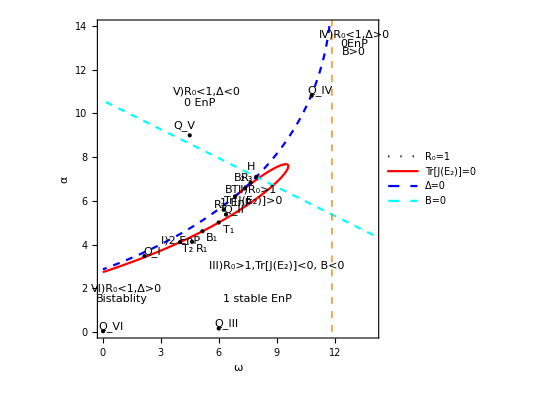

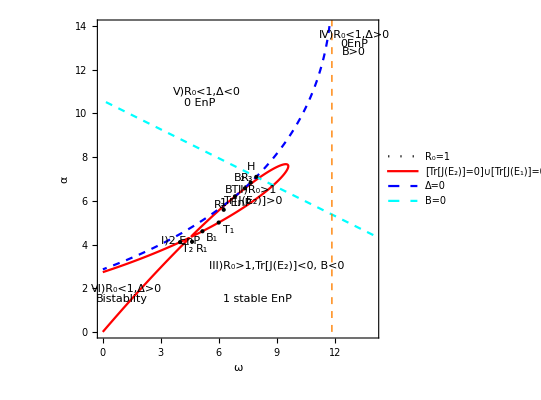

fig6ns.pdf

fig62.pdf

```mathematica
(**Fig 6ns/3, Fig62/4 *)
cn=cut
xm=0;ym=0;xM=14;yM=14;
(*μ/(Subscript[v, 1])//.cn//N*)
p1g=Graphics[{Thick,Orange,Dashed,Line[{{μ/(β+μ ξ)//.cn,0},{μ/(β+μ ξ)//.cn,45}}]}];
R0ωa=(R0//.cn/.η->α/ω);
disωa=(dis/.ceta//.cn);
Bbωa=(B/.ceta//.cn);
trωa=(trE2/.ceta//.cn);
(*Print[" numer is nutr="]*)
nutr=Factor[Numerator[tri]];
rest=Resultant[poli,nutr,i];
trω2=((rest)/.ceta//.cn);

trω=((trG//.cv1)/.ceta//.cn);
ptr=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},PlotPoints -> 200,  
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
  ptr2=ContourPlot[trω2==0,{ω,xm,xM},{α,ym,yM},PlotPoints -> 290, 
 MaxRecursion -> 2, WorkingPrecision -> 35, ContourStyle->{Red},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"[Tr[J(E_2)]=0]∪[Tr[J(E_1)]=0]"}];
 
 
Print["dis at BTP is "]
Chop[Evaluate[disωa//.testBTP//N]]
Print["Dis at H ="]
dis//.testHP//N

pR0=ContourPlot[R0ωa==1,{ω,xm,xM},{α,ym,yM},ContourStyle->{Black,Dotted},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"R_0=1"}];
 
pD=ContourPlot[disωa==0,{ω,xm,xM},{α,ym,yM},
ContourStyle->{ Blue,Dashed}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},
PlotLegends->{"Δ=0"}];

pB=ContourPlot[Bbωa==0,{ω,xm,xM},{α,ym,yM},
ContourStyle->{Dashed,Cyan}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"B=0"}];

 epi= {Black,Style[Text["V)R_0<1,Δ<0",{5.4,11}],13],Style[Text["0 EnP",{5,10.5}],13],
Style[Text["Tr[J(E_2)]>0",{7.8,6}],6],Style[Text["II)R_0>1",{8,6.5}],7],Style
[Text["1 EnP",{6.9,5.9}],6],
Style[Text["IV)R_0<1,Δ>0",{13,13.6}],10],Style[Text["0EnP",{13,13.2}],12],
Style[Text["B>0",{13,12.8}],12],
Style[Text[" VI)R_0<1,Δ>0",{1.2,2}],10],Style[Text["Bistablity",{1,1.5}],10],
Style[Text[" I)2 EnP",{4,4.2}],7],
Style[Text[" III)R_0>1,Tr[J(E_2)]<0, B<0",{9,3}],13],
Style[Text["1 stable EnP",{8,1.5}],13]};

PH=Text["H",Offset[{-5,10},{ω,η ω}//.testHP]];PHp={PointSize[Medium],Style[Point[{ω,η ω}
//.testHP],Yellow]};
PBT=Text["BT",Offset[{-3,6},{ω,α}//.testBTP//N]];PBTp={PointSize[Medium],Style[Point[
{ω,α}//.testBTP//N],Red]};
BP1=Text["B_1",Offset[{10,-7},{ω,α}//.BP[[1]]]];BP1p={PointSize[Medium],Style[Point[
{ω,α}//.BP[[1]]],Green]};
BP2=Text["B_2",Offset[{-5,10},{ω,α}//.BP[[2]]]];BP2p={PointSize[Medium],Style[Point[
{ω,α}//.BP[[2]]],Blue]};
P1=Text["R_1",Offset[{10,-7},{ω,α}//.testR1]];P1p={PointSize[Medium],Style[Point[
{ω,α}//.testR1],Purple]};
(*P4=Text["R_4",Offset[{10,-7},{ω,α}//.testR4]];P4p={PointSize[Medium],
Style[Point[{ω,α}//.testR4],Purple]};*)
P3=Text["R_3",Offset[{-4,5},({ω,α}//.testR3)]];
P3p={PointSize[Medium],Style[Point[{ω,α}//.testR3],Purple]};
P2=Text["R_2",Offset[{-4,5},{ω,α}//.testR2]];
P2p={PointSize[Medium],Style[Point[{ω,α}//.testR2],Purple]};
QI=Text["Q_I",Offset[{8,5},{ω,α}//.test[RI]]];QIp={PointSize[Medium],Style[Point[
{ω,α}//.test[RI]],Magenta]};
QII=Text["Q_II",Offset[{8,5},{ω,α}//.test[II]]];QIIp={PointSize[Medium],Style[Point[
{ω,α}//.test[II]],Magenta]};
QIII=Text["Q_III",Offset[{8,5},{ω,α}//.test[III]]];QIIIp={PointSize[Medium],Style[Point[
{ω,α}//.test[III]],Magenta]};
QIV=Text["Q_IV",Offset[{8,5},{ω,α}//.test[IV]]];QIVp={PointSize[Medium],Style[Point[
{ω,α}//.test[IV]],Magenta]};
QV=Text["Q_V",Offset[{-5,10},{ω,α}//.test[V]]];QVp={PointSize[Medium],Style[Point[
{ω,α}//.test[V]],Magenta]};
QVI=Text["Q_VI",Offset[{8,5},{ω,α}//.test[VI]]];QVIp={PointSize[Medium],
Style[Point[{ω,α}//.test[VI]],Magenta]};
QVIa=Text["Q_VIa",Offset[{8,5},{ω,α}//.test[VIa]]];QVIap={PointSize[Medium],
Style[Point[{ω,α}//.test[VIa]],Magenta]};
T1=Text["T_1",Offset[{10,-7},{ω,α}//.testBoIIandIII]];T1a={PointSize[Medium],
Style[Point[{ω,α}//.testBoIIandIII],Black]};
T2=Text["T_2",Offset[{8,-7},{ω,α}//.testBoIandVIa]];T2a={PointSize[Medium],
Style[Point[{ω,α}//.testBoIandVIa],Black]};
regions={RI,II,III,IV,V,VI};
pt=Table[{ω,α}//.test[j],{j,regions}];
pG=Table[Text[P[j],Offset[{-5,10},pt[[j]]]],{j,6}];

epiP={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p,P1,P1p,P3,P3p,P2,P2p,(*P4,P4p,*)QI,QIp,QII,
QIIp,QIII,QIIIp,QIV,QIVp,QV,QVp,QVI,QVIp,T1,T1a,T2,T2a}//N;
epiP1={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p,P1,P1p,P3,P3p,P2,P2p,T1,T1a,T2,T2a}//N;
fig6F=Show[{pR0,ptr,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epi,epiP},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
fig62=Show[{pR0,ptr2,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epi,epiP1},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]

Export["fig6ns.pdf",fig6F]
Export["fig62.pdf",fig62]
```

#### Blow-up of the Map:

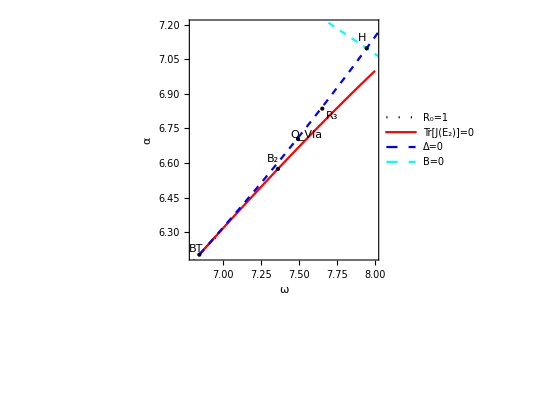

fig6BT.pdf

```mathematica
(*xm=6.8;ym=6.25;xM=7.8;yM=6.9;*)
xm=6.8;ym=6.2;xM=8;yM=7.2;
trωa=((trE2//.cv1)/.ceta//.cn);
ptr=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},PlotPoints -> 200,
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
 P3=Text["R_3",Offset[{10,-7},{ω,α}//.testR3]];
 P3p={PointSize[Medium],Style[Point[{ω,α}//.testR3],Purple]};
 epiP1={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p,P1,P1p,P3,P3p,QVIa,QVIap}//N;
fig6F=Show[{pR0,ptr,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epiP1},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
Export["fig6BT.pdf",fig6F]
```

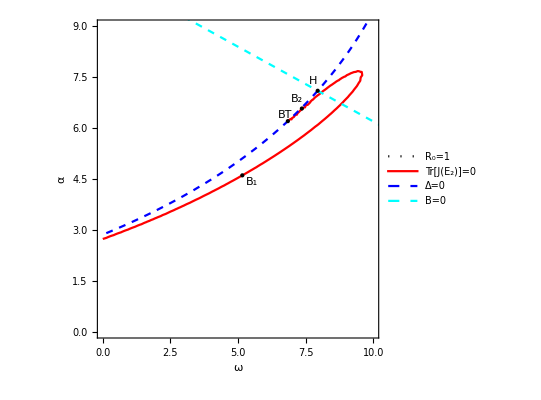

fig6n.pdf

```mathematica
(*xm=6.8;ym=6.25;xM=7.8;yM=6.9;*)
xm=0;ym=0;xM=10;yM=9;
epiP={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p}//N;
trωa=((trE2//.cv1)/.ceta//.cn);
ptr=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
 
fig6F=Show[{pR0,ptr,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epiP},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
Export["fig6n.pdf",fig6F]
```